Zadatak 1. U tabeli su data pobednička vremena ženske plivačke štafete 4 x 100m slobodnim stilom.
		OI | 1996 | 2000 | 2004 | 2012 | 2016
vreme | 3:39.29 | 3:36.61 | 3:35.94 | 3:33.15 | 3:30.65
a) Naći polinom koji interpolira ove podatke.
b) Nacrtati ove podatke i interpolacioni polinom, zajedno na jednom grafiku.
c) Pomoću dobijenog polinoma proceniti pobedničko vreme na OI 2008. Ako je poznato da je na tim OI pobedničko vreme bilo 3:33.76, naći apsolutnu i relativnu grešku ove aproksimacije.

```mathematica
cv={{1996,3*60+39.29},{2000,3*60+36.61},{2004,3*60+35.94},{2012,3*60+33.15},{2016,3*60+30.65}}
```

{{1996,219.29},{2000,216.61},{2004,215.94},{2012,213.15},{2016,210.65}}

```mathematica
pv[t_]=InterpolatingPolynomial[cv,t]//Expand
```

3.5602×10^9-7.09018×10^6 t+5295.03 t^2-1.75749 t^3+0.00021875 t^4

```mathematica
gr1=Plot[pv[t],{t,1996,2016}];
```

```mathematica
gr2=ListPlot[cv];
```

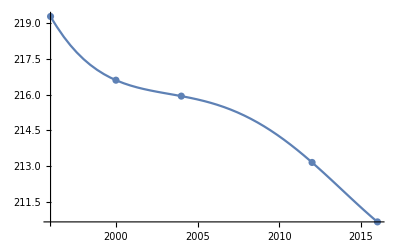

```mathematica
Show[gr1,gr2]
```

```mathematica
vreme=pv[2008];
```

```mathematica
vreme
```

215.074

```mathematica
ag=Abs[vreme-(3*60+33.76)];
```

```mathematica
rg=ag/(3*60+33.76);
```

```mathematica
ag
```

1.314

```mathematica
rg
```

0.00614708

Zadatak 2. Napisati program koji za zadati skup od n+1 čvorova kreira interpolacioni polinom n-tog stepena u obliku p(x)=a_0+a_1 x+a_2 x^2+...+a_n x^n. Program testirati na problemu iz prethodnog zadatka.

```mathematica
cv={{0,3*60+39.29},{4,3*60+36.61},{8,3*60+35.94},{16,3*60+33.15},{20,3*60+30.65}}
```

{{0,219.29},{4,216.61},{8,215.94},{16,213.15},{20,210.65}}

```mathematica
zad2[cv_,x_]:=Module[{},
m=Length[cv];
a=Table[1,{i,1,m},{j,1,m}];
b=Table[cv[[i,2]],{i,1,m}];
Do[
a[[i,j]]=(cv[[i,1]])^(j-1),
{i,1,m},{j,2,m}
];
koef=LinearSolve[a,b];
baza=Table[x^(i-1),{i,1,m}];
koef.baza
]
```

```mathematica
zad2[cv,x]
```

219.29-1.18908 x+0.17025 x^2-0.0109948 x^3+0.00021875 x^4

Zadatak 3. Napisati program koji za zadati skup od n+1 čvorova kreira Lagranžov interpolacioni polinom n-tog stepena, ispisuje ga i iscrtava taj polinom, zajedno sa čvorovima. Program testirati na skupu {(1,2.2),(2,3.6),(4,8),(5,9),(7,11)}.

```mathematica
cv={{1,2.2},{2,3.6},{4,8},{5,9},{7,11}}
```

{{1,2.2},{2,3.6},{4,8},{5,9},{7,11}}

```mathematica
zad3[cv_,x]:=Module[{},
m=Length[cv];
w=1;
Do[
w=w*(x-cv[[i,1]]),
{i,1,m}
];
pol=0;
Do[
wi=w/(x-cv[[i,1]]);
pol=pol+cv[[i,2]]*wi/(wi /.x->cv[[i,1]]),
{i,1,m}
];
pol
]
```

```mathematica
zad3[cv,x]
```

0.0305556 (-7+x) (-5+x) (-4+x) (-2+x)-0.12 (-7+x) (-5+x) (-4+x) (-1+x)+4/9 (-7+x) (-5+x) (-2+x) (-1+x)-3/8 (-7+x) (-4+x) (-2+x) (-1+x)+11/180 (-5+x) (-4+x) (-2+x) (-1+x)

```mathematica
lp[x_]=zad3[cv,x]
```

0.0305556 (-7+x) (-5+x) (-4+x) (-2+x)-0.12 (-7+x) (-5+x) (-4+x) (-1+x)+4/9 (-7+x) (-5+x) (-2+x) (-1+x)-3/8 (-7+x) (-4+x) (-2+x) (-1+x)+11/180 (-5+x) (-4+x) (-2+x) (-1+x)

```mathematica
lp[2.8]
```

5.54829